```mathematica
(*Clean stuff*)
ClearAll["Global`*"]
```

## Probability Declarations

```mathematica
probUnifom[x_, xmin_, xmax_]:=HeavisideTheta[x-xmin] HeavisideTheta[xmax-x];
probUniformNeg[x_, xmin_, xmax_, a_, b_]:=probUnifom[x, a, xmin] + probUnifom[x, xmax, b];
```

## Algorithm

```mathematica
(*Interval Lengths a, b*) 
a=0;
b= 10;
(*Central and sigma value for N1*)
σ = 0.25;


pltRange = {{a-1, b+1}, {0,1.5}}

randomGenNb = 0;

(*Initial uniform probability*)
P0  =1/(b-a);
InitialProb =1/(b-a)*probUnifom[x,a, b];
μ=RandomReal[{a, b}];
PD2=ProbabilityDistribution[InitialProb,{x,a,b}];


complementPDF = 0;
newSigma = 1;

Monitor[
While [ randomGenNb≤300,


If[ 0.9≤ Sin[μ] ≤ 1,
Print["Found one!"];

complementPDFAux = complementPDF;
newSigmaAux=newSigma;

combPDFres2 = addToStepDist[complementPDFAux, newSigmaAux, μ, σ];

complementPDF =combPDFres2[[ 1 ]];
newSigma = combPDFres2[[ 2 ]];


(*complementPDF = complementPDF + probUnifom[x,  μ-(σ/10), μ+(σ/10)];*)




(*newArea2 =Quiet[ NIntegrate[complementPDF, {x, 1, b}]];
rescFact2 = 1/newArea2;

complementPDF = rescFact2 * complementPDF ;*)

lineStyle={Green,Dashed};
minusσline = Line[{{μ - σ,0},{μ-σ,100}}];
plusσline = Line[{{μ + σ,0},{μ+σ,100}}];


posProbPlot =Plot[
complementPDF, {x, a, b},  
PlotStyle->Thick, PlotLegends->"Expressions",
PlotRange->pltRange,
ImageSize->Large, 
Filling->Axis
];

probPlot =Show[
Plot[{ PDF2, InitialProb, 1/(b-a)}, {x,a,b},
PlotStyle->Thick, PlotLegends->"Expressions",
PlotRange->pltRange,
Epilog->{Directive[lineStyle], minusσline, plusσline, Green,PointSize@Large,
	       Point[{μ,0.001}] },
ImageSize->Large,  Filling->Axis
]
(*,
Histogram[data,50,"ProbabilityDensity",  PlotRange->pltRange]*)
];
randomGenNb ++; 
Print[Style["Sampling from the new PDF.",Blue]];

μ = RandomVariate[PD2];
Print[Style["Done Sampling.",Blue]];
(*Pause[1];*)

,


DentingProb =  probUniformNeg[x, μ-σ, μ+σ, a, b];
newArea =Quiet[ NIntegrate[InitialProb * DentingProb, {x, 1, b}]];
rescFact = 1/newArea;



PDF2=rescFact*InitialProb * DentingProb;
(*totalProb = Quiet[ NIntegrate[PDF2, {x, a, b}]];
Print["Checking that the total probability is : ", totalProb];*)


PD2=ProbabilityDistribution[PDF2,{x,a,b}];
(*data=RandomVariate[PD2,10^5];*)


(*Print ["New Random Variate", newRandomVariate];*)




(*{Red,PointSize@Large,Point[{μ,0}]}*)

lineStyle={Red,Dashed};
(*lineStyle2={Blue,Dashed};
lineStyle3={Blue,Dashed};*)


minusσline = Line[{{μ - σ,0},{μ-σ,100}}];
plusσline = Line[{{μ + σ,0},{μ+σ,100}}];

(*complementPD=ProbabilityDistribution[complementPDF,{x,a,b}];
dataProb=RandomVariate[complementPD,10^5];
*)
posProbPlot = 
Plot[
complementPDF, {x, a, b},  
PlotStyle->Thick, PlotLegends->"Expressions",
ImageSize->Large,
PlotRange->pltRange,
Filling->Axis
];


probPlot =Show[
Plot[{ PDF2, InitialProb, 1/(b-a)}, {x,a,b},
PlotStyle->Thick, PlotLegends->"Expressions",
PlotRange->pltRange,
Epilog->{Directive[lineStyle], minusσline, plusσline, Red,PointSize@Large,
	       Point[{μ,0.001}] },
ImageSize->Large, Filling->Axis
]
(*,
Histogram[data,50,"ProbabilityDensity",  PlotRange->pltRange]*)
];

InitialProb = PDF2;
μ = RandomVariate[PD2];

randomGenNb ++; 
(*Pause[1];*)
]	
]
, {probPlot, posProbPlot}]
Print[probPlot, posProbPlot]
```

```mathematica
addToStepDist[probToAdd_,probHeight_, μ2_, σ2_]:=Module[
{ PDF2, combPDF, newSigma, newArea, rescalingFactor},
Print ["Inside the adding function."];

PDF2 = 1/(2σ2)*probUnifom[x, μ2-σ2, μ2+σ2];



rescFactAux = probHeight / (1/(2σ2));

If[probToAdd == 0,

(*Print["In the case!!!"];*)

Return[{PDF2,1/(2σ2), PDF2 }];
];

(*Print ["Don't have a 0 probability therefore fun time."];
Print[PDF2];*)
PDF2 = PDF2 * rescFactAux;
(*Print [rescFactAux];
Print [PDF2];*)

combPDF = probToAdd + PDF2-1/probHeight probToAdd * PDF2;

Print[Style["Integrating the new PDF.",Red]];
newArea = probHeight * (2σ2) - Quiet[ NIntegrate[1/probHeight probToAdd * PDF2, {x, 1, 10}]];
(*newArea =Quiet[ NIntegrate[combPDF, {x, 1, 10}]];*)
rescalingFactor = 1/newArea;
combPDF = rescalingFactor * combPDF;


Print["Checking the new probability is : ", Quiet[ NIntegrate[combPDF, {x, 1, 10}]]];
Print["Done with the adding function"];


Return [{combPDF, rescalingFactor * probHeight, PDF2 }];
]
```

Inside the adding function.

Integrating the new PDF.

Done with the adding function

The total probability of thw new PDF is: 1.

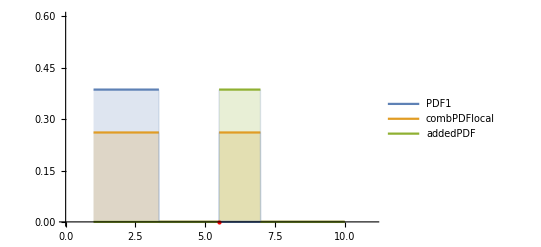

Inside the adding function.

Integrating the new PDF.

Done with the adding function

The total probability of thw new PDF is: 1.

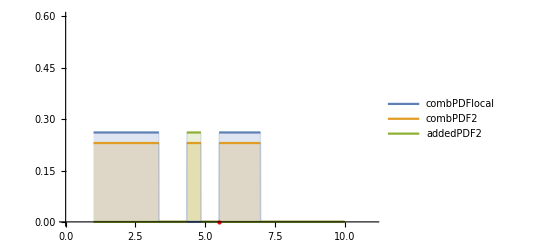

```mathematica
ClearAll["PDF1, combPDFres"]
pltRange = {{a-1, b+1}, {0,0.6}};
a= 1;
b=10;

μ1=RandomReal[{a+1, b-1}];
μ2=RandomReal[{a+1, b-1}];
σ1 = 1.294;
σ2 = 0.744;



(*PDF1 = 0;*)
PDF1 = RandomChoice [{0, 1/(2σ1)*probUnifom[x, μ1-σ1, μ1+σ1] }];
(*PDF2 = 1/(2σ2)*probUnifom[x, μ2-σ2, μ2+σ2];
Print ["Total probability of PDF1 is : ",Quiet[ NIntegrate[PDF1, {x, 1, 10}]] ]
Print ["Total probability of PDF2 is : ",Quiet[ NIntegrate[PDF2, {x, 1, 10}]] ]

rescFactAux = (σ2) / (σ1);
PDF2 = PDF2 * rescFactAux;


combPDF = PDF1 + PDF2- (2σ1)*PDF1 * PDF2;
newArea =Quiet[ NIntegrate[combPDF, {x, 1, 10}]];

rescalingFactor = 1/newArea;
combPDF = rescalingFactor * combPDF;
Print ["Total probability of the combined PDF is : ",Quiet[ NIntegrate[combPDF, {x, 1, 10}]] ]*)
currentHeight = 1/(2σ1);


combPDFres= addToStepDist[PDF1, currentHeight, μ2, σ2];
combPDFlocal = combPDFres[[ 1]];
addedPDF = combPDFres[[3]];

newHeight = combPDFres[[ 2 ]];

Print ["The total probability of thw new PDF is: ", Quiet[ NIntegrate[combPDFlocal, {x, 1, 10}]]];



Plot[
{PDF1,   combPDFlocal,addedPDF}, {x, 1, 10}, Filling->Axis, PlotLegends->"Expressions", PlotStyle->Thick,
Epilog->{ Red,PointSize@Large,   Point[{μ2-σ2,0.001}]},
PlotRange->pltRange
]

μ3=RandomReal[{a+1, b-1}];
σ3 = 0.2554;


combPDFres2 = addToStepDist[combPDFlocal, newHeight, μ3, σ3];
combPDF2 = combPDFres2[[ 1 ]];
addedPDF2 = combPDFres2 [[ 3 ]];

Print ["The total probability of thw new PDF is: ", Quiet[ NIntegrate[combPDF2, {x, 1, 10}]]];

Plot[
{combPDFlocal, combPDF2, addedPDF2}, {x, 1, 10}, Filling->Axis, PlotLegends->"Expressions", PlotStyle->Thick,
Epilog->{ Red,PointSize@Large,   Point[{μ2-σ2,0.001}]},
PlotRange->pltRange
]
```